```mathematica
λ=0.575*I+0.01625;
soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z]
z1=z/.soluciones[[1]]
z2=z/.soluciones[[2]]
z3=z/.soluciones[[3]]
```

{{z→0.00879457+0.357847 ⅈ},{z→0.0139752-0.316729 ⅈ},{z→0.0683617+2.54286 ⅈ}}

0.00879457+0.357847 ⅈ

0.0139752-0.316729 ⅈ

0.0683617+2.54286 ⅈ

```mathematica
p[z_]:=(z^2-1)(z-λ);lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z];
iterSch= Compile[{{z,_Complex}},sp[z]];
r1=1;r2=-1;r3=λ;
Clear[rootPosition]
rootPosition[z_]:= 
Which[Abs[z - r1] <  10.0^(-6), 3,
	       Abs[z - r2] <  10.0^(-6), 2,
	       Abs[z -r3] <  10.0^(-6), 1,
	       True, 0]
Clear[iterColorAlgorithm,colorLevel,fractalColor,plotColorFractal]
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
Block[{z,ct,r}, z = x + y I; ct = 0;r = rootPosition[z];
While[(r==0) && (ct < lim),++ct;
z = iterMethod[z];r = rootPosition[z]
];
If[Head[r]==Which,r =0]; (* "Which" unevaluated *)
Return[N[r+ct/(lim+0.001)]]
]
colorLevelWS= Compile[{{p,_Real}},0.4*FractionalPart[p]];
fractalColorWS[p_] :=
Block[{pp = colorLevelWS[p]},
Switch[IntegerPart[p],
3, CMYKColor[0.6+pp,0.,0.,2*pp],
2, CMYKColor[0.,0.6+pp,0.,2*pp],
1, CMYKColor[0.,0.,0.6+pp,2*pp],
0, CMYKColor[0.,0.,0.,1.]
]
]
ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,4},(* Three roots *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
```

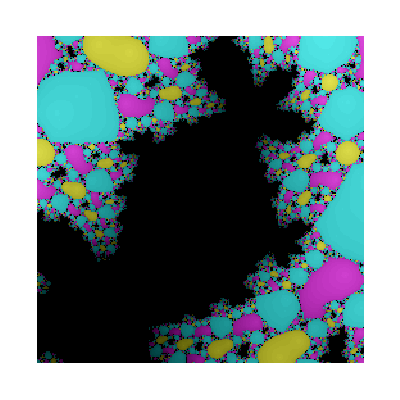

```mathematica
numberPoints =254;
limIterations=50;
xxMin=Re[z2]-1; xxMax=Re[z2]+1; yyMin=Im[z2]-1; yyMax=Im[z2]+1;
plotColorFractal[iterSch, numberPoints]
```

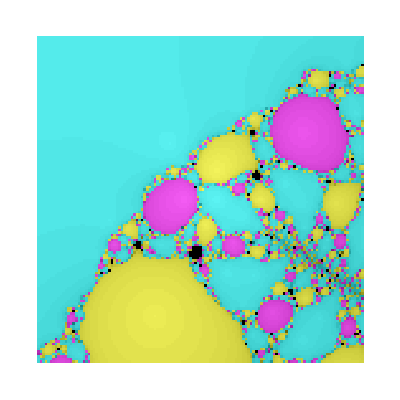

```mathematica
numberPoints =128;
limIterations=50;
xxMin=-10; xxMax=10; yyMin=-10; yyMax=10;
plotColorFractal[iterSch, numberPoints]
```

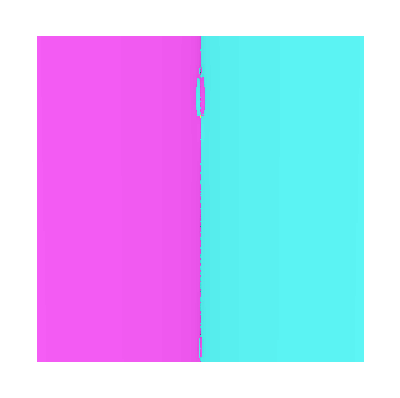

```mathematica
numberPoints =256;
limIterations=100;
xxMin=-0.25; xxMax=0.25; yyMin=0.25; yyMax=0.32;
plotColorFractal[iterSch, numberPoints]
```

```mathematica
NestList[sp,z1,100]
```

{0.00879457+0.357847 ⅈ,0.0146576+0.558073 ⅈ,0.0162017+0.574763 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ}

```mathematica
NestList[sp,z2,100]
```

{0.0139752-0.316729 ⅈ,1.51498-7.43422 ⅈ,0.0423022+0.35982 ⅈ,0.0150163+0.556595 ⅈ,0.0162081+0.574719 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ,0.01625+0.575 ⅈ}

```mathematica
NestList[sp,z3,500]
```

{0.0683617+2.54286 ⅈ,0.015326-0.0746467 ⅈ,0.146472+4.12561 ⅈ,0.0146888-0.0289913 ⅈ,0.0291006+2.27115 ⅈ,0.0163944-0.0699186 ⅈ,0.0553012+3.84186 ⅈ,0.0121893-0.0390225 ⅈ,0.118277+2.53908 ⅈ,0.015324-0.0747744 ⅈ,0.147495+4.13388 ⅈ,0.0147032-0.028708 ⅈ,0.0284075+2.26412 ⅈ,0.0164485-0.0696391 ⅈ,0.0510605+3.82594 ⅈ,0.0120759-0.0395914 ⅈ,0.1235+2.55571 ⅈ,0.0154165-0.07478 ⅈ,0.141518+4.13488 ⅈ,0.014498-0.0286886 ⅈ,0.0334708+2.26339 ⅈ,0.0162437-0.0695925 ⅈ,0.0626388+3.82243 ⅈ,0.012491-0.0396888 ⅈ,0.111326+2.55995 ⅈ,0.015409-0.0747145 ⅈ,0.141559+4.13057 ⅈ,0.0145098-0.0288346 ⅈ,0.0333616+2.26703 ⅈ,0.0162379-0.0697406 ⅈ,0.0635966+3.83093 ⅈ,0.0125054-0.0393879 ⅈ,0.109977+2.55096 ⅈ,0.0153705-0.0747258 ⅈ,0.144135+4.13104 ⅈ,0.0145961-0.0288124 ⅈ,0.0311898+2.26658 ⅈ,0.0163268-0.0697293 ⅈ,0.0584274+3.83064 ⅈ,0.0123243-0.0394095 ⅈ,0.115467+2.55105 ⅈ,0.015379-0.0747492 ⅈ,0.143748+4.13262 ⅈ,0.0145792-0.0287598 ⅈ,0.0315468+2.26526 ⅈ,0.0163166-0.0696744 ⅈ,0.0587876+3.82744 ⅈ,0.0123442-0.0395213 ⅈ,0.11522+2.55447 ⅈ,0.0153939-0.0747423 ⅈ,0.142728+4.13228 ⅈ,0.0145454-0.0287739 ⅈ,0.032403+2.26557 ⅈ,0.0162809-0.0696843 ⅈ,0.0608836+3.82786 ⅈ,0.012417-0.0395017 ⅈ,0.112976+2.5541 ⅈ,0.0153883-0.0747332 ⅈ,0.143032+4.13165 ⅈ,0.0145572-0.0287946 ⅈ,0.0321341+2.26609 ⅈ,0.0162902-0.0697065 ⅈ,0.0604416+3.82918 ⅈ,0.0123985-0.0394564 ⅈ,0.113392+2.55269 ⅈ,0.0153829-0.0747374 ⅈ,0.143409+4.13188 ⅈ,0.0145695-0.0287857 ⅈ,0.0318197+2.26589 ⅈ,0.0163036-0.0696991 ⅈ,0.0596414+3.82881 ⅈ,0.0123712-0.0394712 ⅈ,0.114256+2.55305 ⅈ,0.0153859-0.0747406 ⅈ,0.143235+4.13211 ⅈ,0.014563-0.0287784 ⅈ,0.0319708+2.2657 ⅈ,0.016298-0.069691 ⅈ,0.0599265+3.82832 ⅈ,0.0123823-0.0394878 ⅈ,0.113974+2.55358 ⅈ,0.0153878-0.0747384 ⅈ,0.143101+4.13198 ⅈ,0.0145588-0.028783 ⅈ,0.032082+2.26581 ⅈ,0.0162932-0.0696951 ⅈ,0.0602223+3.82854 ⅈ,0.0123922-0.0394795 ⅈ,0.113651+2.55336 ⅈ,0.0153863-0.0747374 ⅈ,0.143192+4.13191 ⅈ,0.014562-0.0287854 ⅈ,0.032004+2.26587 ⅈ,0.0162962-0.0696979 ⅈ,0.0600634+3.82871 ⅈ,0.0123862-0.0394737 ⅈ,0.113812+2.55317 ⅈ,0.0153857-0.0747384 ⅈ,0.143235+4.13197 ⅈ,0.0145633-0.0287832 ⅈ,0.0319686+2.26582 ⅈ,0.0162978-0.0696959 ⅈ,0.0599628+3.8286 ⅈ,0.0123829-0.0394779 ⅈ,0.113924+2.55328 ⅈ,0.0153864-0.0747387 ⅈ,0.143192+4.13199 ⅈ,0.0145618-0.0287825 ⅈ,0.0320056+2.2658 ⅈ,0.0162963-0.069695 ⅈ,0.0600418+3.82854 ⅈ,0.0123858-0.0394798 ⅈ,0.113842+2.55335 ⅈ,0.0153866-0.0747383 ⅈ,0.14318+4.13196 ⅈ,0.0145615-0.0287835 ⅈ,0.0320153+2.26583 ⅈ,0.0162959-0.0696959 ⅈ,0.060073+3.8286 ⅈ,0.0123868-0.0394778 ⅈ,0.113807+2.55329 ⅈ,0.0153862-0.0747382 ⅈ,0.143199+4.13196 ⅈ,0.0145622-0.0287837 ⅈ,0.0319987+2.26583 ⅈ,0.0162965-0.0696962 ⅈ,0.0600361+3.82861 ⅈ,0.0123855-0.0394773 ⅈ,0.113846+2.55327 ⅈ,0.0153862-0.0747384 ⅈ,0.143202+4.13197 ⅈ,0.0145622-0.0287832 ⅈ,0.0319969+2.26582 ⅈ,0.0162966-0.0696957 ⅈ,0.0600281+3.82859 ⅈ,0.0123853-0.0394782 ⅈ,0.113855+2.5533 ⅈ,0.0153864-0.0747384 ⅈ,0.143193+4.13197 ⅈ,0.0145619-0.0287832 ⅈ,0.032004+2.26582 ⅈ,0.0162963-0.0696957 ⅈ,0.0600445+3.82859 ⅈ,0.0123858-0.0394782 ⅈ,0.113838+2.5533 ⅈ,0.0153863-0.0747383 ⅈ,0.143193+4.13197 ⅈ,0.0145619-0.0287834 ⅈ,0.0320038+2.26582 ⅈ,0.0162963-0.0696959 ⅈ,0.0600456+3.8286 ⅈ,0.0123859-0.0394779 ⅈ,0.113836+2.55329 ⅈ,0.0153863-0.0747383 ⅈ,0.143197+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.0320009+2.26582 ⅈ,0.0162964-0.0696959 ⅈ,0.0600386+3.8286 ⅈ,0.0123856-0.0394779 ⅈ,0.113844+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143196+4.13197 ⅈ,0.014562-0.0287833 ⅈ,0.0320013+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600391+3.82859 ⅈ,0.0123856-0.039478 ⅈ,0.113843+2.5533 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287833 ⅈ,0.0320025+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600419+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.11384+2.5533 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.0320021+2.26582 ⅈ,0.0162964-0.0696959 ⅈ,0.0600413+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143196+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.0320017+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600403+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113842+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143196+4.13197 ⅈ,0.014562-0.0287833 ⅈ,0.0320019+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600406+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113842+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.0320021+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.060041+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143196+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.0320019+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600407+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ,0.0162964-0.0696958 ⅈ,0.0600408+3.82859 ⅈ,0.0123857-0.039478 ⅈ,0.113841+2.55329 ⅈ,0.0153863-0.0747384 ⅈ,0.143195+4.13197 ⅈ,0.014562-0.0287834 ⅈ,0.032002+2.26582 ⅈ}